# リンゴ樹の具体例 ver1

-Graphics-

```mathematica
リンゴの樹の大きさや発育は主に「台木」の部分で決まる→台木の種類の違いによって樹の成長に与える効果をみたい！

・１列目のローマ数字が同じもの同士は、台木が同一の木のクローンであるグループ(接ぎ木に使った木の種類は全て同じ)
　→接ぎ木は穂木、台木から形成されているが
・樹の成長の方法は２通り①胴回りの成長（２列と４列）②芽の伸び（３列）
・地上部分の重量（５列）
```

リンゴの樹の大きさや発育は主に「台木」の部分で決まる→台木の種類の違いによって樹の成長に与える効果をみたい！

接ぎ木に使った木の種類は全て同じ ・１列目のローマ数字が同じもの同士は、台木が同一の木のクローンであるグループ

Syntax::sntxf: ""の後に"\:30f3\:30b4\:306e\:6a39\:306e\:5927\:304d\:3055\:3084\:767a\:80b2\:306f\:4e3b\:306b\:300c\:53f0\:6728\:300d\:306e\:90e8\:52
      06\:3067\:6c7a\:307e\:308b→台木の種類の違いによって樹の成長\:30
      6b\:4e0e\:3048\:308b\:52b9\:679c\:3092\:307f\:305f\:3044\:ff01"が続くことはできません．

接ぎ木は穂木、台木から形成されているが

・樹の成長の方法は２通り①胴回りの成長（２列と４列）②芽の伸び（３列）

・地上部分の重量（５列）

## 準備

```mathematica
SetDirectory["/Users/kuzubatomohiko/Library/Mobile Documents/com~apple~CloudDocs/.Trash/OneDrive - Kyoto University/M1/多変量解析/樹木データ"]
```

/Users/kuzubatomohiko/Library/Mobile Documents/com~apple~CloudDocs/.Trash/OneDrive - Kyoto University/M1/多変量解析/樹木データ

```mathematica
"/Users/kuzubatomohiko/Documents/M1/多変量解析/樹木データ"
```

/Users/kuzubatomohiko/Documents/M1/多変量解析/樹木データ

```mathematica
data=Import["Classical_Apple_Experiment.csv"];
data//MatrixForm
root = data[[;;,1]];(*品種*)
trunk4 = data[[;;,2]]; (*4年経った木の胴回りの長さmm*)
growth4=data[[;;,3]] ;(*高さcm*)
trunk15=data[[;;,4]]; (*15年経った木の胴回りの長さmm*)
weight15=data[[;;,5]]/2.2046 ; (*重量pond->kg*)
```

(I | 111 | 2569 | 358 | 760
I | 119 | 2928 | 375 | 821
I | 109 | 2865 | 393 | 928
I | 125 | 3844 | 394 | 1009
I | 111 | 3027 | 360 | 766
I | 108 | 2336 | 351 | 726
I | 111 | 3211 | 398 | 1209
I | 116 | 3037 | 362 | 750
II | 105 | 2074 | 409 | 1036
II | 117 | 2885 | 406 | 1094
II | 111 | 3378 | 487 | 1635
II | 125 | 3906 | 498 | 1517
II | 117 | 2782 | 438 | 1197
II | 115 | 3018 | 465 | 1244
II | 117 | 3383 | 469 | 1495
II | 119 | 3447 | 440 | 1026
III | 107 | 2505 | 376 | 912
III | 99 | 2315 | 444 | 1398
III | 106 | 2667 | 438 | 1197
III | 102 | 2390 | 467 | 1613
III | 115 | 3021 | 448 | 1476
III | 120 | 3085 | 478 | 1571
III | 120 | 3308 | 457 | 1506
III | 117 | 3231 | 456 | 1458
IV | 122 | 2838 | 389 | 944
IV | 103 | 2351 | 405 | 1241
IV | 114 | 3001 | 405 | 1023
IV | 101 | 2439 | 392 | 1067
IV | 99 | 2199 | 327 | 693
IV | 111 | 3318 | 395 | 1085
IV | 120 | 3601 | 427 | 1242
IV | 108 | 3291 | 385 | 1017
V | 91 | 1532 | 404 | 1084
V | 115 | 2552 | 416 | 1151
V | 114 | 3083 | 479 | 1381
V | 105 | 2330 | 442 | 1242
V | 99 | 2079 | 347 | 673
V | 122 | 3366 | 441 | 1137
V | 105 | 2416 | 464 | 1455
V | 113 | 3100 | 457 | 1325
VI | 111 | 2813 | 376 | 800
VI | 75 | 840 | 314 | 606
VI | 105 | 2199 | 375 | 790
VI | 102 | 2132 | 399 | 853
VI | 105 | 1949 | 334 | 610
VI | 107 | 2251 | 321 | 562
VI | 113 | 3064 | 363 | 707
VI | 111 | 2469 | 395 | 952
VII | 96 | 2091 | 266 | 414
VII | 91 | 1583 | 241 | 335
VII | 120 | 4099 | 380 | 885
VII | 110 | 3383 | 401 | 1012
VII | 102 | 2785 | 296 | 489
VII | 105 | 2785 | 315 | 616
VII | 110 | 3387 | 358 | 788
VII | 108 | 3082 | 343 | 733
IX | 83 | 1344 | 231 | 375
IX | 90 | 2247 | 250 | 410
IX | 87 | 1426 | 219 | 335
IX | 94 | 2211 | 275 | 560
IX | 69 | 877 | 205 | 251
IX | 84 | 1431 | 213 | 272
IX | 90 | 1863 | 266 | 478
IX | 90 | 2001 | 226 | 278
X | 105 | 1964 | 299 | 506
X | 117 | 2516 | 381 | 882
X | 113 | 3016 | 362 | 737
X | 113 | 3424 | 372 | 772
X | 122 | 3174 | 369 | 827
X | 109 | 2865 | 368 | 821
X | 117 | 3634 | 408 | 1149
X | 122 | 3393 | 410 | 1035
XII | 129 | 4387 | 431 | 1609
XII | 135 | 4166 | 465 | 1658
XII | 138 | 4595 | 484 | 1789
XII | 142 | 5131 | 527 | 2375
XII | 132 | 4041 | 463 | 1556
XII | 123 | 3848 | 412 | 1418
XII | 142 | 5471 | 514 | 2266
XII | 144 | 5956 | 522 | 2508
XIII | 121 | 3705 | 387 | 1052
XIII | 120 | 2886 | 414 | 1167
XIII | 123 | 3856 | 387 | 981
XIII | 109 | 2763 | 390 | 944
XIII | 100 | 2223 | 327 | 737
XIII | 116 | 2905 | 424 | 1392
XIII | 117 | 3590 | 421 | 1326
XIII | 105 | 2516 | 382 | 1052
XV | 122 | 3484 | 448 | 1258
XV | 116 | 2730 | 435 | 1304
XV | 124 | 3924 | 451 | 1290
XV | 122 | 3580 | 450 | 1288
XV | 125 | 3355 | 428 | 1176
XV | 122 | 3694 | 424 | 1177
XV | 126 | 4698 | 482 | 1331
XV | 119 | 3566 | 469 | 1490
XVI | 126 | 4299 | 452 | 1499
XVI | 113 | 3432 | 412 | 1412
XVI | 113 | 3357 | 425 | 1488
XVI | 138 | 5475 | 460 | 1751
XVI | 127 | 4482 | 464 | 1937
XVI | 115 | 3333 | 457 | 1823
XVI | 120 | 3960 | 463 | 1838
XVI | 119 | 4040 | 473 | 1817)

```mathematica
index=DeleteDuplicates[root](*rootの種類一覧を作りたい*)
```

{I,II,III,IV,V,VI,VII,IX,X,XII,XIII,XV,XVI}

```mathematica
MatrixForm[Transpose[Table[{n,index[[n]]},{n,1,Length[index]}]]]
```

(1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13
I | II | III | IV | V | VI | VII | IX | X | XII | XIII | XV | XVI)

```mathematica
Position[{a,b,a,a,b,c,b},b](*positionの使い方:bの位置について聞く*)
```

{{2},{5},{7}}

```mathematica
Position[root,index[[1]]](*Ⅰの場所を教えて*)
```

{{1},{2},{3},{4},{5},{6},{7},{8}}

```mathematica
trunk15[Position[root,index[[1]]]]//Flatten(*Iの場所にある数字教えて*)
```

{358,375,393,394,360,351,398,362,409,406,487,498,438,465,469,440,376,444,438,467,448,478,457,456,389,405,405,392,327,395,427,385,404,416,479,442,347,441,464,457,376,314,375,399,334,321,363,395,266,241,380,401,296,315,358,343,231,250,219,275,205,213,266,226,299,381,362,372,369,368,408,410,431,465,484,527,463,412,514,522,387,414,387,390,327,424,421,382,448,435,451,450,428,424,482,469,452,412,425,460,464,457,463,473}[{{1},{2},{3},{4},{5},{6},{7},{8}}]

```mathematica
extract[data_,indexnum_]:=data[[Position[root,index[[indexnum]]]//Flatten]]
```

```mathematica
extract[trunk15,1]
```

{358,375,393,394,360,351,398,362}

## 可視化

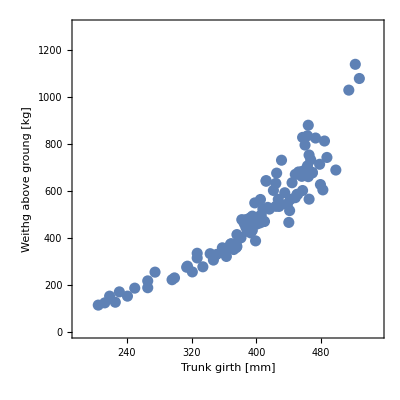

```mathematica
p0 =ListPlot[Transpose[{trunk15, weight15}], AspectRatio->1,Frame->True,
PlotStyle->PointSize[0.02],
PlotRange->{{180,550},{0,1300}},
FrameLabel->{Style["Trunk girth [mm]",Black,16],Style["Weithg above groung [kg]",Black,16]}]
```

```mathematica
Manipulate[ListPlot[Transpose[{extract[trunk15,n],extract[ weight15,n]}], AspectRatio->1,Frame->True,
PlotStyle->PointSize[0.02],
PlotRange->{{180,550},{0,1300}},
FrameLabel->{{Style["Trunk girth [mm]",Black,16],""},{Style["Weithg above groung [kg]",Black,16],Style["Root: "<>ToString[index[[n]]],Black,20]}}],
{n,1,13, Appearance->True}]
```

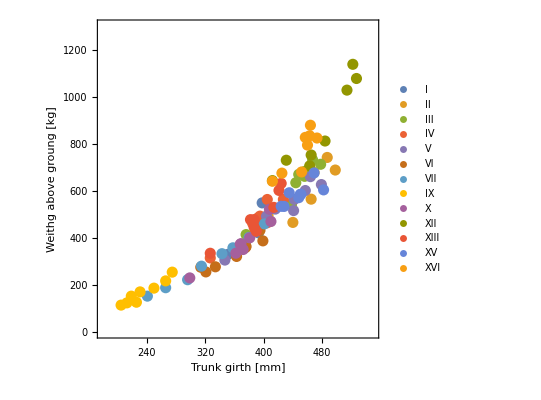

```mathematica
ListPlot[Table[Transpose[{extract[trunk15,n],extract[weight15,n]}],{n,1,13}], AspectRatio->1,Frame->True,
PlotLegends->index,
PlotStyle->PointSize[0.02],
PlotRange->{{180,550},{0,1300}},
FrameLabel->{Style["Trunk girth [mm]",Black,16],Style["Weithg above groung [kg]",Black,16]}]
```

```mathematica
weightdist=FindDistribution[weight15]
```

NormalDistribution[502.44,216.416]

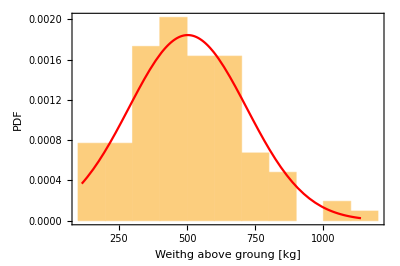

```mathematica
weighthist1=Plot[PDF[weightdist,x],{x,Min[weight15],Max[weight15]},PlotStyle->Red];
weighthist2=Histogram[weight15,"Sturges","PDF",AspectRatio->2/3,Frame->True,
FrameLabel->{{Style["PDF",Black,16],""},{Style["Weithg above groung [kg]",Black,16],Style["Histogram of weight15",Black,20]}}];
Show[weighthist2,weighthist1]
```

## 最尤法1: 1次関数モデル

```mathematica
model1[β0_, β1_,x_]:=β0+β1 x;
norm1[β0_, β1_,σ_,x_,y_]:=Exp[-(y-model1[β0, β1,x])^2/(2σ^2)]/(√(2 π) σ);
```

```mathematica
(*最小二乗法でパラメータ推定*)
FindMinimum[Total[(weight15-model1[β0, β1,trunk15])^2],{β0,β1}]
```

{707507.,{β0→-555.857,β1→2.66439}}

```mathematica
(weight15-model1[β0, β1,trunk15]/.%[[2]]).(weight15-model1[β0, β1,trunk15]/.%[[2]])/Length[data]//Sqrt (*sigma*)
```

82.48

```mathematica
(*組み込み関数でパラメータ推定*)
fit1=NonlinearModelFit[Transpose[{trunk15,weight15}], model1[β0, β1,x],{β0,β1},x]
```

FittedModel[-555.857+2.66439 x]

```mathematica
resid1=fit1["FitResiduals"];
```

```mathematica
sigma1=Total[resid1^2]/Length[data]//Sqrt (*sigma*)
```

82.48

```mathematica
FindDistribution[resid1]
```

ExtremeValueDistribution[-37.5198,66.1159]

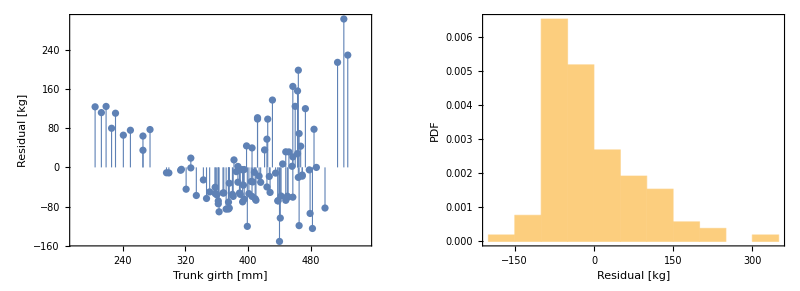

```mathematica
p11=ListPlot[Transpose[{trunk15,resid1}],Filling->Axis,AspectRatio->2/3,Frame->True,
PlotStyle->PointSize[0.013],
FillingStyle->Thickness[0.002],
PlotRange->{{180,550},All},
FrameLabel->{{Style["Residual [kg] ",Black,16],""},{Style["Trunk girth [mm]",Black,16],Style["Residual Plot",Black,20]}}];
p12=Histogram[resid1,"Sturges","PDF",AspectRatio->2/3,Frame->True,
FrameLabel->{{Style["PDF",Black,16],""},{Style["Residual [kg]",Black,16],Style["Histgram of Residuals",Black,20]}}];
GraphicsRow[{p11,p12}]
```

```mathematica
(*最尤法でパラメータ推定*)
(*ギモン： 初期値の設定の仕方どうしたら良いか…現在は最小二乗法の推定結果から初期値を決め打ちしている*)
loglik1=FindMaximum[{Total[Log[norm1[β0,β1,σ,trunk15,weight15]]],σ>0},{{β0,-555},{β1,3},{σ,100}}]
```

{-606.475,{β0→-555.857,β1→2.66439,σ→82.48}}

```mathematica
(*AIC*)
aic1=-2*loglik1[[1]]+2*3
```

1218.95

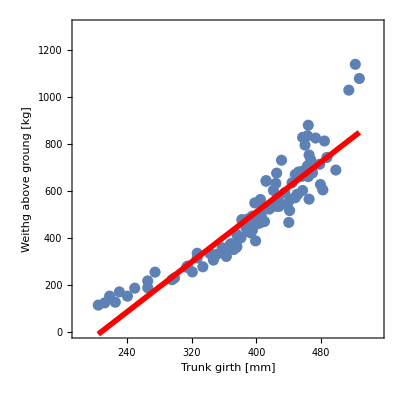

```mathematica
p13=Plot[fit1[x],{x,Min[trunk15],Max[trunk15]}, PlotStyle->{Red,Thickness[0.01]}];
Show[p0,p13]
```

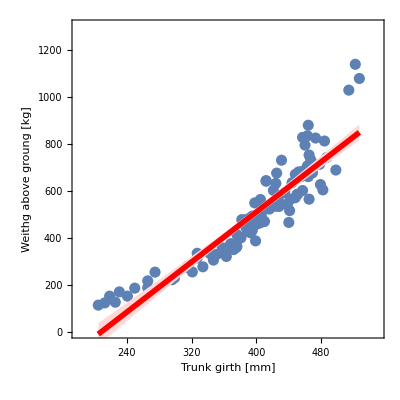

```mathematica
fit1ci95[x_]:=fit1["MeanPredictionBands",ConfidenceLevel->.95];
p14=Plot[{fit1[x],fit1ci95[x]},{x,Min[trunk15],Max[trunk15]}, Filling->{2->{1}},PlotStyle->{{Red,Thickness[0.01]},None},FillingStyle->LightRed];
Show[p0,p14]
```

## 最尤法2: 2次関数モデル

```mathematica
model2[β0_, β1_,β2_,x_]:=β0+β1 x + β2 x^2;
norm2[β0_, β1_,β2_,σ_,x_,y_]:=Exp[-(y-model2[β0, β1,β2,x])^2/(2σ^2)]/(√(2 π) σ);
```

```mathematica
(*最小二乗法でパラメータ推定*)
FindMinimum[Total[(weight15-model2[β0, β1,β2,trunk15])^2],{β0,β1,β2}]
```

{450251.,{β0→429.492,β1→-2.94336,β2→0.00763261}}

```mathematica
(weight15-model2[β0,β1,β2,trunk15]/.%[[2]]).(weight15-model2[β0, β1,β2,trunk15]/.%[[2]])/Length[data]//Sqrt (*sigma*)
```

65.7977

```mathematica
(*組み込み関数でパラメータ推定*)
fit2=NonlinearModelFit[Transpose[{trunk15,weight15}], model2[β0, β1,β2,x],{β0,β1,β2},x]
```

FittedModel[429.492-2.94336 x+0.00763261 x^2]

```mathematica
resid2=fit2["FitResiduals"];
```

```mathematica
sigma2=Total[resid2^2]/Length[data]//Sqrt (*sigma*)
```

65.7977

```mathematica
FindDistribution[resid2]
```

MixtureDistribution[{0.317286,0.624534,0.0581803},{UniformDistribution[{-180.253,171.665}],NormalDistribution[-10.6376,29.4725],NormalDistribution[77.9744,40.2689]}]

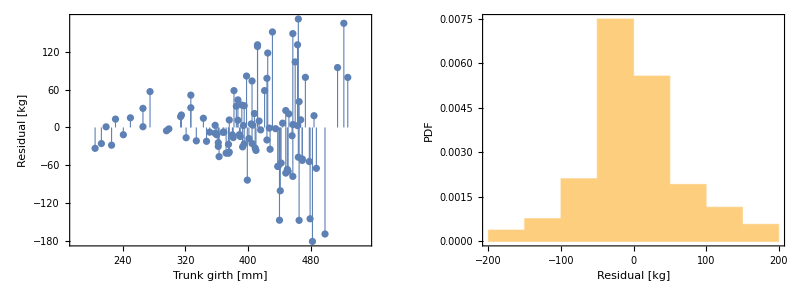

```mathematica
p21=ListPlot[Transpose[{trunk15,resid2}],Filling->Axis,AspectRatio->2/3,Frame->True,
PlotStyle->PointSize[0.013],
FillingStyle->Thickness[0.002],
PlotRange->{{180,550},All},
FrameLabel->{{Style["Residual [kg] ",Black,16],""},{Style["Trunk girth [mm]",Black,16],Style["Residual Plot",Black,20]}}];
p22=Histogram[resid2,"Sturges","PDF",AspectRatio->2/3,Frame->True,
FrameLabel->{{Style["PDF",Black,16],""},{Style["Residual [kg]",Black,16],Style["Histgram of Residuals",Black,20]}}];
GraphicsRow[{p21,p22}]
```

```mathematica
(*最尤法でパラメータ推定*)
(*ギモン： 初期値の設定の仕方どうしたら良いか…現在は最小二乗法の推定結果から初期値を決め打ちしている*)
loglik2=FindMaximum[{Total[Log[norm2[β0,β1,β2,σ,trunk15,weight15]]],σ>0},{{β0,429},{β1,-3},{β2,0.007},{σ,100}}]
```

{-582.974,{β0→429.492,β1→-2.94336,β2→0.00763261,σ→65.7977}}

```mathematica
(*AIC*)
aic2=-2*loglik2[[1]]+2*4
```

1173.95

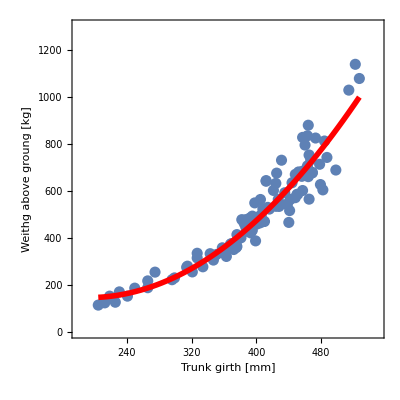

```mathematica
p23=Plot[fit2[x],{x,Min[trunk15],Max[trunk15]}, PlotStyle->{Red,Thickness[0.01]}];
Show[p0,p23]
```

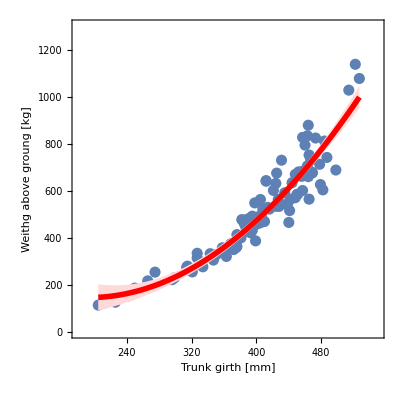

```mathematica
fit2ci95[x_]:=fit2["MeanPredictionBands",ConfidenceLevel->.95];
p24=Plot[{fit2[x],fit2ci95[x]},{x,Min[trunk15],Max[trunk15]}, Filling->{2->{1}},PlotStyle->{{Red,Thickness[0.01]},None},FillingStyle->LightRed];
Show[p0,p24]
```

## 最尤法3: 指数関数モデル

```mathematica
model3[β0_, β1_,x_]:= Exp[β0+β1 x];
norm3[β0_, β1_,σ_,x_,y_]:=Exp[-(y-model3[β0, β1,x])^2/(2σ^2)]/(√(2 π) σ);
```

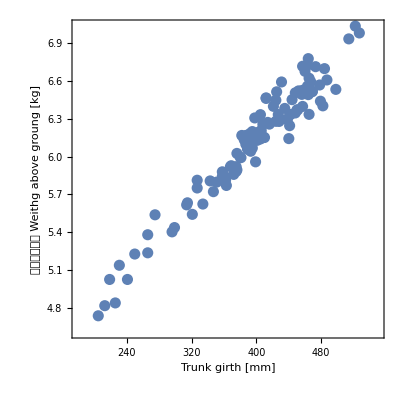

```mathematica
p30=ListPlot[Transpose[{trunk15, Log[weight15]}], AspectRatio->1,Frame->True,
PlotStyle->PointSize[0.02],
PlotRange->{{180,550},All},
FrameLabel->{Style["Trunk girth [mm]",Black,16],Style["対数変化した   Weithg above groung [kg]",Black,16]}]
```

```mathematica
fit3log=FindFit[Transpose[{trunk15, Log[weight15]}],β0+β1 x,{β0,β1},x]
```

{β0→3.54399,β1→0.00649026}

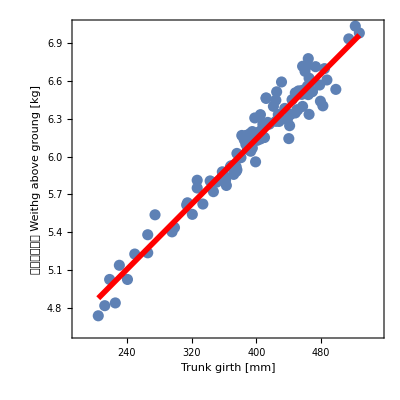

```mathematica
Show[p30,Plot[β0+β1 x/.fit3log,{x,Min[trunk15],Max[trunk15]}, PlotStyle->{Red,Thickness[0.01]}]]
```

```mathematica
(*最小二乗法でパラメータ推定*)
FindMinimum[Total[(weight15-model3[β0, β1,trunk15])^2],{β0,{β1,0.005}},WorkingPrecision->50]
```

FindMinimum::precw: 引数関数((113.853-ⅇ^(β0+205 β1))^2+(123.378-ⅇ^(β0+213 β1))^2+(151.955-ⅇ^(β0+219 β1))^2+(126.1-ⅇ^(β0+226 β1))^2+(170.099-ⅇ^(β0+231 β1))^2+(151.955-ⅇ^(β0+241 β1))^2+(185.975-ⅇ^(β0+250 β1))^2+«37»+(457.679-ⅇ^(β0+394 β1))^2+(431.824-ⅇ^(β0+395 β1))^2+(492.153-ⅇ^(β0+395 β1))^2+(548.399-ⅇ^(β0+398 β1))^2+(386.918-ⅇ^(β0+399 β1))^2+(459.04-ⅇ^(β0+401 β1))^2+«53»)の精度がWorkingPrecision (50.)より小さくなっています．

FindMinimum::precw: 引数関数({1.4142135623730950488016887242096980785696718753769 (113.852853125283-2.71828182845905^(β0+205 β1)),1.4142135623730950488016887242096980785696718753769 (123.378390637757-2.71828182845905^(β0+213 β1)),«48»,«53»})の精度がWorkingPrecision (50.)より小さくなっています．

FindMinimum::sszero: 検索の刻み幅がPrecisionGoalオプションで特定されている許容度よりも小さくなりましたが，勾配はAccuracyGoalオプションで特定されている許容度よりも大きいです．最小値でない点で，この方法では立ち往生している可能性があります．

{439859.25559194427579228213768744448763925447565271,{β0→3.6223550879223152535558777743005799046193218838738,β1→0.0063188778786302673904405443094170525644582513543915}}

```mathematica
(weight15-model3[β0, β1,trunk15]/.%[[2]]).(weight15-model3[β0, β1,trunk15]/.%[[2]])/Length[data]//Sqrt (*sigma*)
```

65.034

```mathematica
(*組み込み関数でパラメータ推定*)
(*微妙に値が異なる…*)
fit3=NonlinearModelFit[Transpose[{trunk15,weight15}], model3[β0, β1,x],{β0,{β1,0.00649}},x]
```

FittedModel[ⅇ^(3.62236+0.00631888 x)]

```mathematica
resid3=fit3["FitResiduals"];
```

```mathematica
sigma3=Total[resid3^2]/Length[data]//Sqrt (*sigma*)
```

65.034

```mathematica
FindDistribution[resid3]
```

LaplaceDistribution[-0.352022,48.9994]

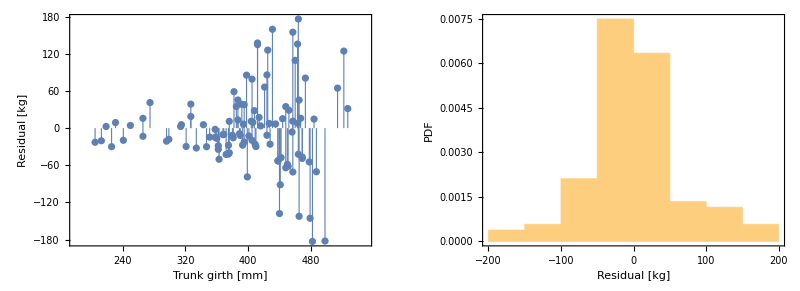

```mathematica
p31=ListPlot[Transpose[{trunk15,resid3}],Filling->Axis,AspectRatio->2/3,Frame->True,
PlotStyle->PointSize[0.013],
FillingStyle->Thickness[0.002],
PlotRange->{{180,550},All},
FrameLabel->{{Style["Residual [kg] ",Black,16],""},{Style["Trunk girth [mm]",Black,16],Style["Residual Plot",Black,20]}}];
p32=Histogram[resid3,"Sturges","PDF",AspectRatio->2/3,Frame->True,
FrameLabel->{{Style["PDF",Black,16],""},{Style["Residual [kg]",Black,16],Style["Histgram of Residuals",Black,20]}}];
GraphicsRow[{p31,p32}]
```

```mathematica
(*最尤法でパラメータ推定*)
(*ギモン： 初期値の設定の仕方どうしたら良いか…現在は最小二乗法の推定結果から初期値を決め打ちしている*)
loglik3=FindMaximum[{Total[Log[norm3[β0,β1,σ,trunk15,weight15]]],σ>0},{{β0,3.6},{β1,0.0064},{σ,100}}]
```

{-581.76,{β0→3.62236,β1→0.00631888,σ→65.034}}

```mathematica
(*AIC*)
aic3=-2*loglik3[[1]]+2*3
```

1169.52

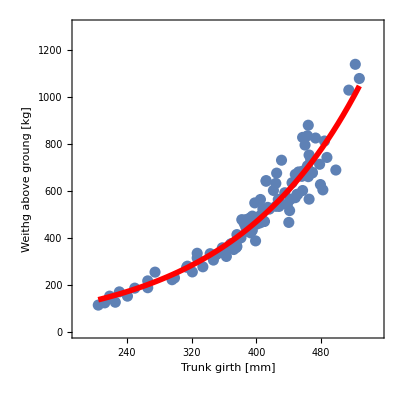

```mathematica
p33=Plot[fit3[x],{x,Min[trunk15],Max[trunk15]}, PlotStyle->{Red,Thickness[0.01]}];
Show[p0,p33]
```

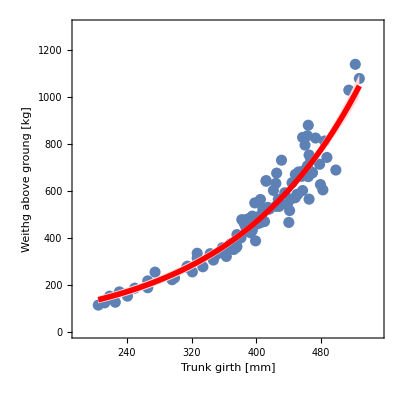

```mathematica
fit3ci95[x_]:=fit3["MeanPredictionBands",ConfidenceLevel->.95];
p34=Plot[{fit3[x],fit3ci95[x]},{x,Min[trunk15],Max[trunk15]}, Filling->{2->{1}},PlotStyle->{{Red,Thickness[0.01]},None},FillingStyle->LightRed];
Show[p0,p34]
```

## モデル選択

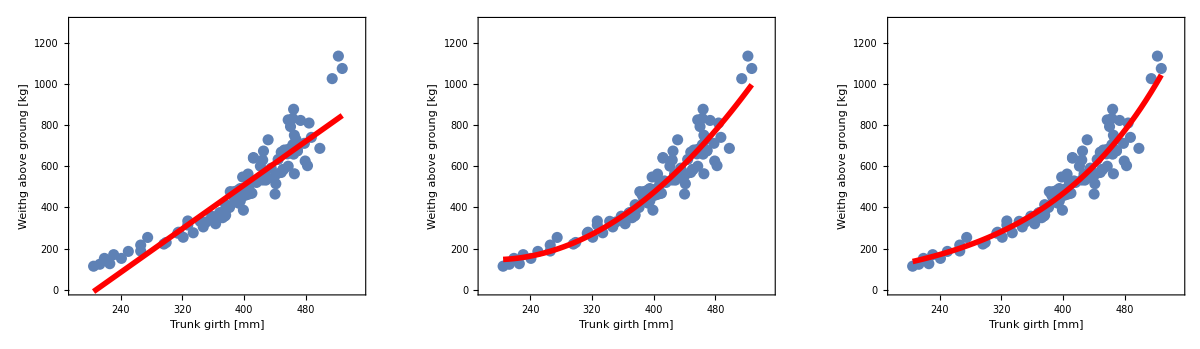

```mathematica
GraphicsRow[{Show[p0,p13],Show[p0,p23],Show[p0,p33]}]
```

```mathematica
summary=Transpose[{{"linear","quadratic", "exponential"},{aic1, aic2, aic3},{sigma1,sigma2,sigma3}}]//Prepend[{"model","AIC","sigma"}];
Grid[summary, Dividers->{False,All},ItemStyle-> 18, Spacings->{10, 1},Alignment->{Left,Right,Right}]
```

model | AIC | sigma
linear | 1218.95 | 82.48
quadratic | 1173.95 | 65.7977
exponential | 1169.52 | 65.034